```mathematica
ClearAll["Global`*"]
```

```mathematica
q:=(1-p)
v:=1-u
fun= 2*(p q*p^2*(1-v^2)) + p^2*(p^4(1-v^4) + 2(p^2(1-v^2)))-u
Collect[fun, p]
Solve[fun==0 , p]//FullSimplify
```

p^2 (2 p^2 (1-(1-u)^2)+p^4 (1-(1-u)^4))+2 (1-p) p^3 (1-(1-u)^2)-u

2 p^3 (1-(1-u)^2)+p^6 (1-(1-u)^4)-u

{{p→(1/(2-u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)},{p→-(-1)^(1/3) (1/(2-u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)},{p→(-1)^(2/3) (1/(2-u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)},{p→(-1/(-2+u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)},{p→-(-1)^(1/3) (-1/(-2+u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)},{p→(-1)^(2/3) (-1/(-2+u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)}}

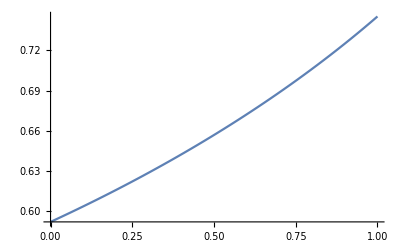

1/(2+2 √2)^(1/3)

0.59165

```mathematica
pv[u_]:=(1/(2-u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)
Plot[pv[x],{x,0,1}]
pv[0]
pv[0]//N
```

```mathematica
(1/(2-u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)//FullSimplify
```

(1/(2-u+√(-((-2+u) (4+(-3+u) u)))))^(1/3)